```mathematica
Needs["VariationalMethods`"]
Quit;
ClearAll;
```

```mathematica
Action=Sqrt[-(r[ϕ]^2-m[v[ϕ]]/r[ϕ]^2)v'[ϕ]^2+(2r'[ϕ]v'[ϕ])/(r[ϕ]^2-m[v[ϕ]])+r[ϕ]^2];
```

```mathematica
FullSimplify[Eliminate[{EulerEquations[Action,v[ϕ],ϕ],EulerEquations[Action,r[ϕ],ϕ],r[ϕ]^4/r0^2==-((r[ϕ]^2-m[v[ϕ]])/r[ϕ]^2)v'[ϕ]^2+(2r'[ϕ]v'[ϕ])/(r[ϕ]^2-m[v[ϕ]])+r[ϕ]^2},m[v[ϕ]]]] (*We can eliminate one of the two EL equaitons using eqn4.6 which can be derived from reparametrrising the action in terms of v and then minimising*)
```

$Aborted

```mathematica
a=1/3; (*Parameter which controls the speed of the perturbation*)
Subscript[m, 0]=1; (*final value of mass function*)
m[v_]:=Subscript[m, 0](Tanh[v/a]+1)/2; (*define the mass function*)
t=6; (*Inital field theory time on boundary*)
rmax=100;
xmax=100;
```

rmin= 0.01

b= 0.980178

vmin= -25.6236

ℓ/2= 30.9784

x @ vmin 30.9784

x @ rmin 30.9784

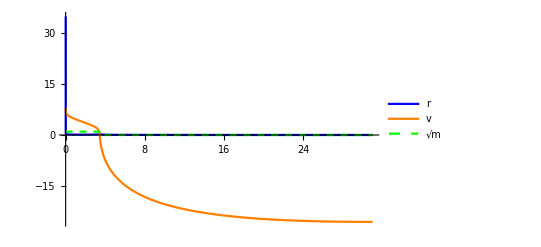

```mathematica
r0=0.01; (*Minimum value of r*)
Eqn1=r0^2(r[ϕ]^4/r0^2==r[ϕ]^2+2 r'[ϕ] v'[ϕ]-(1-(2m[v[ϕ]])/r[ϕ]) v'[ϕ]^2)-r[ϕ]^4; (*the two equations of motion eqns 4.6, 4.7*)
Eqn2=r[ϕ]^3/r0+(r0 v'[ϕ] (-6 r'[ϕ]+v'[ϕ]))/r[ϕ]+2 r0 v''[ϕ]-3 r0 r[ϕ];
x0=r0/(2(rmax)^2); (*x0 must be adjusted wrt to r0 and rmax *)
b=0.980178; (*integration const b, b nonzero for r0<1.0, i.e. inside the Vaidya geometry*)
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t-1/rmax+b/(2 rmax^2),v'[x0]==-rmax/r0+b/r0},{r,v},{x,x0,xmax}];
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]]; (*x=ℓ/2 when r'=v'=0, r[x]=r0,v[x]=v0*)
Print["rmin= ",rmin=First[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["b= ",b]
Print["vmin= ",vmin=First[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["ℓ/2= ",ℓ/2]
Print["x @ vmin ",x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["x @ rmin ",x/.Last[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
ab=Plot[{Evaluate[r[x]/.Sol],Evaluate[v[x]/.Sol],Evaluate[Sqrt[m[v[x]]]/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,Orange,{Dashed,Green}},PlotLegends->{"r","v","√m"}]
```

{7.99005,100.}

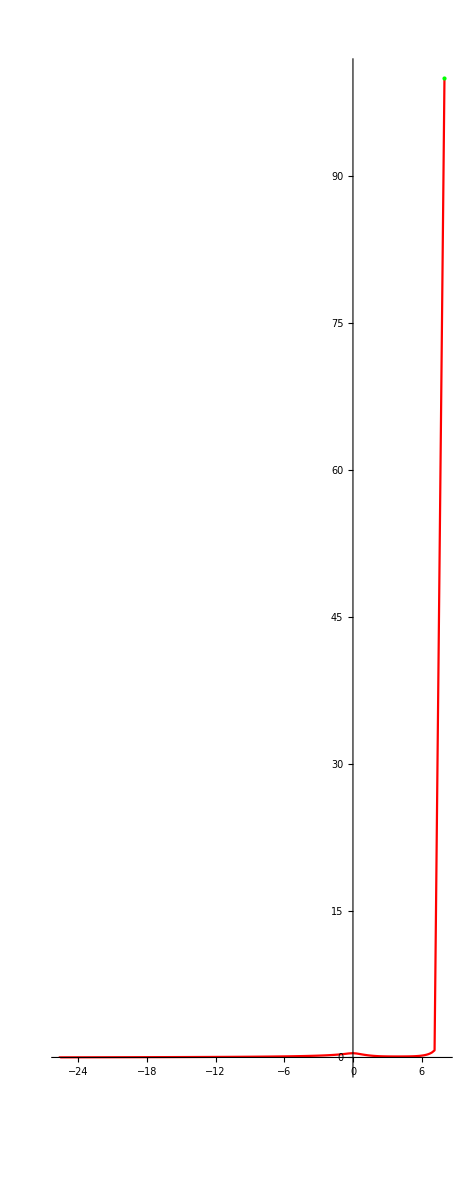

```mathematica
dot={v[x0]/.Sol[[1]],r[x0]/.Sol[[1]]}
ParametricPlot[Evaluate[{v[x],r[x]}/.Sol]/.Sol,{x,x0,ℓ/2},AspectRatio->Full,PlotRange->All,Epilog->{PointSize[Large],Green,Point[dot]},PlotStyle->Red]
```

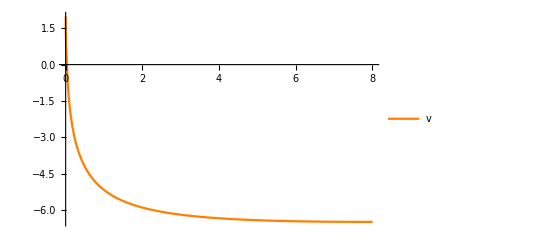

```mathematica
Plot[{Evaluate[v[x]/.Sol]},{x,x0,ℓ/2},PlotRange->All,PlotStyle->{Orange},PlotLegends->{"v"},PlotRange->All]
```

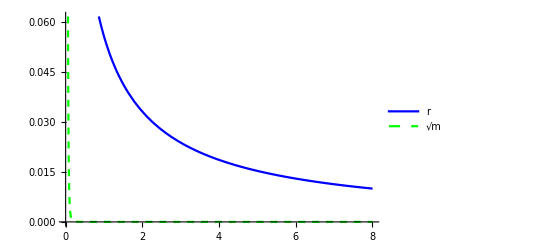

```mathematica
Plot[{Evaluate[r[x]/.Sol],Evaluate[Sqrt[m[v[x]]]/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,{Dashed,Green}},PlotLegends->{"r","√m"}]
```